```mathematica
-------Function behaviour near x=0------
```

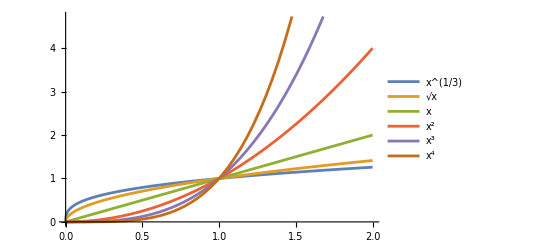

```mathematica
Plot[{x^(1/3),√x,x,x^2,x^3,x^4},{x,0,2},PlotLegends->"Expressions"]
```

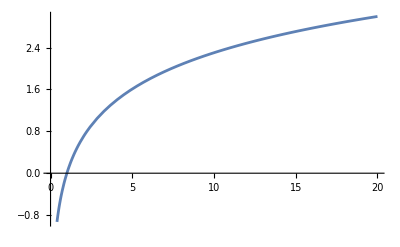

```mathematica
Plot[Log[x],{x,0,20}]
```

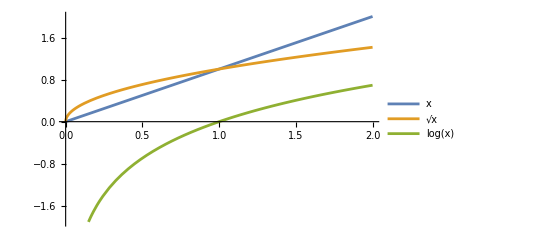

```mathematica
Plot[{x,√x,Log[x]},{x,0,2},PlotLegends->"Expressions"]
```

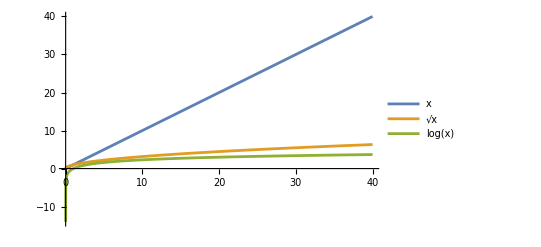

```mathematica
Plot[{x,√x,Log[x]},{x,0,40},PlotLegends->"Expressions"]
```

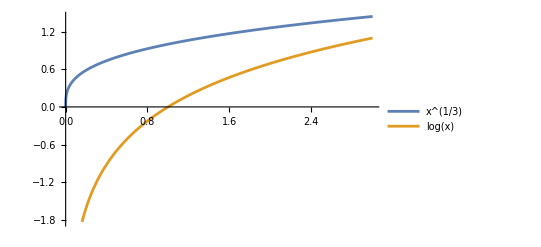

```mathematica
Plot[{x^(1/3),Log[x]},{x,0,3},PlotLegends->"Expressions"]
```

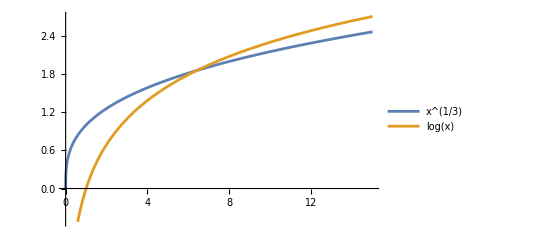

```mathematica
Plot[{x^(1/3),Log[x]},{x,0,15},PlotLegends->"Expressions"]
```

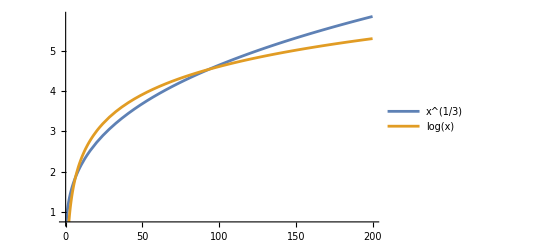

```mathematica
Plot[{x^(1/3),Log[x]},{x,0,200},PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot[{x^(1/n),Log[x]},{x,0,100},PlotLegends->{x^(1/"n"),Log[x]},Frame->True],{{n,2},1,5}]
```

```mathematica
N[E,10]
```

2.718281828

```mathematica
N[E^E,10]
```

15.15426224

```mathematica
------------Finding the fixed points for 1D flow and analysis of its stability---------
```

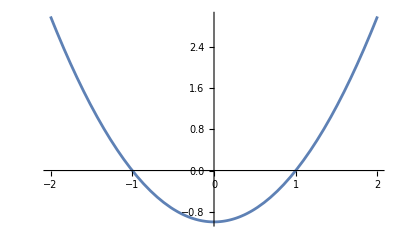

```mathematica
Plot[x^2-1,{x,-2,2}]
```

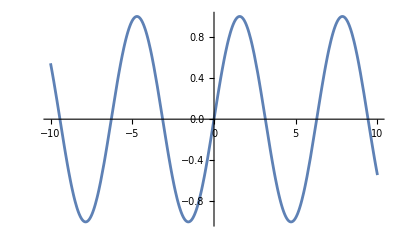

```mathematica
Plot[Sin[x],{x,-10,10}]
```

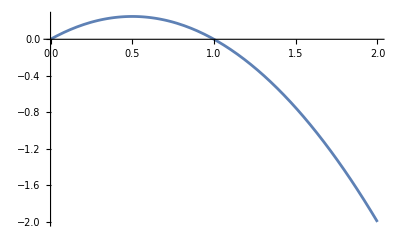

```mathematica
Plot[x(1-x),{x,0,2}]
```

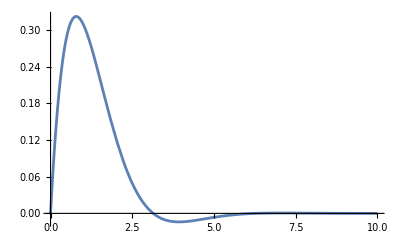

```mathematica
Plot[Exp[-x]Sin[x],{x,0,10}]
```

```mathematica
-------------Bifurcation----------
```

```mathematica
Manipulate[Plot[r+x^2,{x,-10,10},Axes->True,PlotRange->{-10,10}],{r,-10,10}]
```

```mathematica
Manipulate[Plot[1+r x+x^2,{x,-5,5},PlotRange->{-10,10}],{r,-5,5}]
```

```mathematica
Manipulate[Plot[{1+r x+x^2,1-x^2},{x,-20,20},PlotRange->{-50,50}],{r,-10,10}]
```

```mathematica
----------Electric circuit  with  R=1,C=100,V0=10------
```

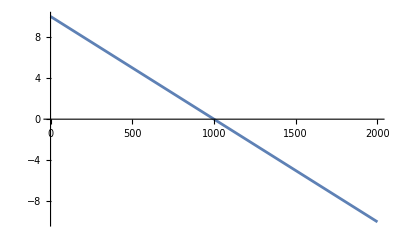

```mathematica
Plot[10-x/100,{x,0,2000}]
```

```mathematica
Manipulate[Plot[v/r-x/(r c),{x,0,3000},PlotRange->Full],{v,10,20},{r,1,5},{c,100,200}]
```

```mathematica
---------Logistc equation  r=1, N=1000-----
```

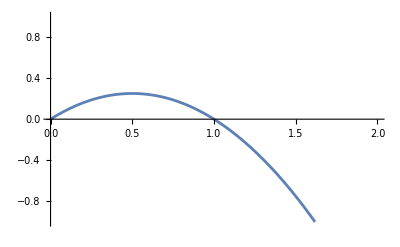

```mathematica
Plot[x(1-x),{x,0,2},PlotRange->{-1,1}]
```

```mathematica
Manipulate[Plot[r x(1-x/k),{x,0,10},PlotRange->{-5,5}],{r,1,2},{k,1,5}]
```

```mathematica
f1= a  x (1-x)
```

a (1-x) x

```mathematica
Manipulate[Plot[f1/.a->a1,{x,0,10}],{a1,0,1}]
```

```mathematica
f1[x]==r x(1-x/k)(*won't work*)
Manipulate[Plot[f1,{x,0,2}],{r,1,2},{k,1,2}]
```

(r x (1-x/k))[x]==r x (1-x/k)

```mathematica
f2=D[f1,x]
```

```mathematica
-(r x)/k+r (1-x/k)

Manipulate[Plot[f1/.r->r1/.k->k1,{x,0,3},PlotRange->Automatic],{r1,1,2},{k1,1,2}]
```

-(r x)/k+r (1-x/k)

```mathematica
Manipulate[Plot[{r-x,Exp[-x]},{x,-10,10},PlotRange->{-10,10}],{r,-5,5}]
```

```mathematica
Manipulate[Plot[{r,Sin[x]},{x,-10,10}],{r,-2,2}]
```

```mathematica
--------Properties of function -------
```

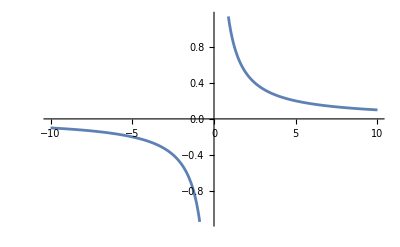

```mathematica
Plot[1/x,{x,-10,10}]
```

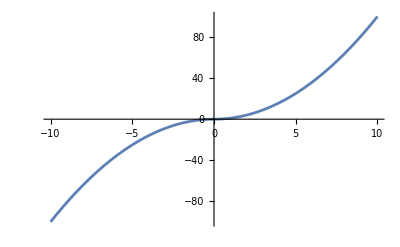

```mathematica
Plot[x Abs[x],{x,-10,10}]
```

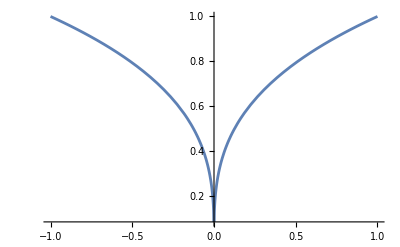

```mathematica
Plot[{Abs[x]^(1/3)},{x,-1,1}]
```

```mathematica
Manipulate[Plot[{a^2/(x^2+a^2)},{x,-5,5},PlotRange->{0,1},PlotLegends->{"Lorentzian"}],{a,0.2,2,0.1}]
```

```mathematica
Manipulate[Plot[{1/(x^2-a^2)},{x,-5,5},PlotRange->Full,PlotLegends->{"1/x^2"},PlotLabel->Style["a"-> a,16,Blue]],{a,0.5,2,0.1}]
```

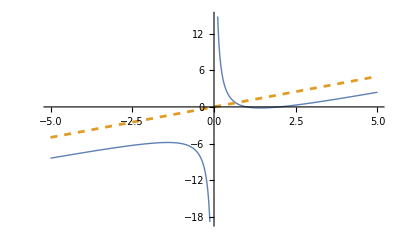

```mathematica
Plot[{(x-1)(x-2)/x,x},{x,-5,5},PlotStyle->{Thick,Dashed}]
```

```mathematica
Manipulate[Plot[{Exp[-x^2/a^2],Exp[-1],a^2/(x^2+a^2),1-x^2/a^2},{x,-5,5},PlotRange->{0,1},PlotLabel->Style["a"-> a,16,Blue],PlotLegends->{"Gaussian","1/e","Lorentzian","Parabola"}],{a,0.5,2,0.1}]
```